```mathematica
<<RiemannHilbert`
```

PainleveII[{s1,s2,s3},x]  evaluates the solution to Painleve II with Stokes' constants s1, s2 and s3 at the point x.  

	It should be accurate for all x less than 5 (it uses a deformed contour for negative x, and should remain accurate as x tends to -∞), except for the special case s1 s3 = 1, which includes the Hastings–McLeod solution.  Future releases will handle this special case, as well as positive x.

	The default accuracy is 10.^(-7), this can be increased using 

		PainleveII[{s1,s2,s3},x,InterpolationPrecision->tol] 
		
Implemention notes:

	For -5 < x, the routine uses the method developed in [Olver 2009b], and should take roughly 5 seconds for the first usage, and less than 2 seconds for any subsequent evaluations.
	
	For x ≤ -5, the routine uses a deformed contour.  To reuse computation, The same contour is used for x lying in intervals of size 5.  Thus, while the first computation in each block takes roughly 27 seconds, subsequent evaluations within the same block of 5 will be significantly faster, around 3.5 seconds.
	
	To speed up the algorithm, we store precomputed matrices.  Evaluate

```mathematica
ClearPainleveDatabase[]
```

To remove these stored matrices and free up the memory.

## Ablowitz–Segur solutions

We compute solutions which are asymptotic to α Ai[z].  This is equivalent to the Stokes' constants (-ⅈ α,0,ⅈ α).

```mathematica
s//Clear;
s[α_]:={-I α,0,I α};
```

We save the computation — in case you wish to extend or refine the graphs without starting from scratch — as the method is still fairly slow

```mathematica
Clear[p];
p[α_,x_]:=p[α,x]=PainleveII[s[α],x]
```

### Example solutions

Two solutions near the Hastings–McLeod solution (but with drasticly different behaviour)

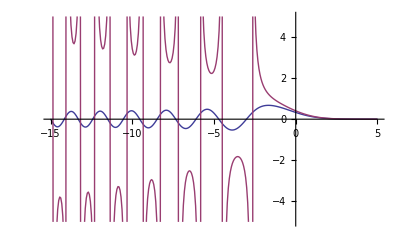

```mathematica
Monitor[TablePlot[{p[.9,x]//Re,p[1.1,x]//Re},{x,-15.,5.,2.^(-4)},PlotRange->{-5,5}],x]
```

Here's two oscillatory solutions for large negative x

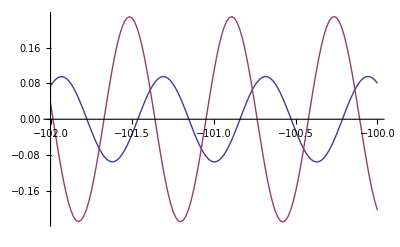

```mathematica
Monitor[TablePlot[{p[.5,x]//Re,p[.9,x]//Re},{x,-102.,-100.,2.^(-6)}],x]
```

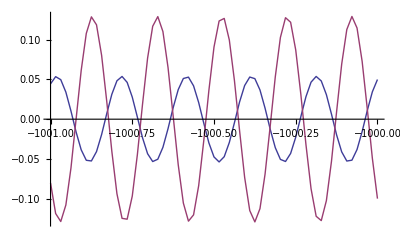

```mathematica
Monitor[TablePlot[{p[.5,x]//Re,p[.9,x]//Re},{x,-1001.,-1000.,2.^(-6)}],x]
```

And here's two exploding solutions for large negative x

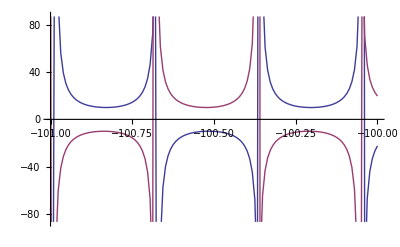

```mathematica
Monitor[TablePlot[{p[1.1,x]//Re,p[1.5,x]//Re},{x,-101.,-100.,2.^(-7)}],x]
```

### Improving accuracy

```mathematica
p[α_,x_,tol_]:=p[α,x,tol]=PainleveII[s[α],x,InterpolationPrecision->tol]
```

Note that the true solution is real, while the computed solution has a small imaginary error:

```mathematica
p[.5,-111.]
```

0.0708778+2.7142×10^-9 ⅈ

The default interpolation precision is 10^-7.  We can improve the accuracy by increasing the precision (at a cost of increased time):

```mathematica
p[.5,-111.,10.^-9]
```

0.0708778+1.59503×10^-11 ⅈ

```mathematica
p[.5,-111.,10.^-11]
```

0.0708778-2.03382×10^-14 ⅈ

```mathematica
p[.5,-111.,10.^-13]
```

0.0708778+3.37419×10^-16 ⅈ

We can plot the convergence:

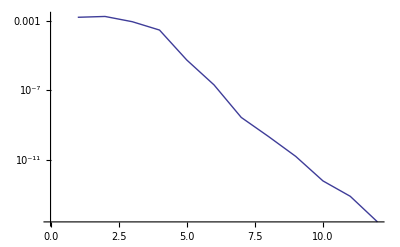

```mathematica
Monitor[TableLogPlot[p[.5,-111.,10.^(-j)]-p[.5,-111.,10.^-13]//Abs,{j,1,12}],j]
```

### Comparison with asymptotics

For 0 < α < 1, we have the following asymptotic approxiamtion:

```mathematica
d[α_]:=Sqrt[-1/π Log[1-α^2]];
θ2[α_]:=π/4-3/2 d[α]^2 Log[2] - Arg[Gamma[1-(I d[α]^2)/2]];
asym[α_,z_]:=d[α](-z)^(-1/4)Sin[2/3(-z)^(3/2)-3/4 d[α]^2 Log[-z]+θ2[α]];
```

We see that the asymptotic approximation is indeed asymptotic to our computed solution

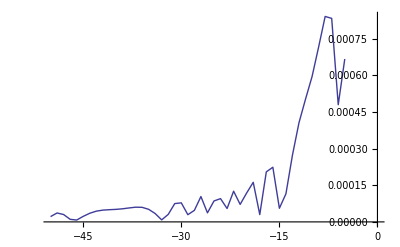

```mathematica
Monitor[TablePlot[(asym[0.5,x]-p[0.5,x])//Abs,{x,-50.,-5.}],x]
```

## Real-valued example

Here's another example where we know for sure that the solution is real

```mathematica
p2[x_]:=p2[x]=PainleveII[{1+I,-2,1-I},x];
```

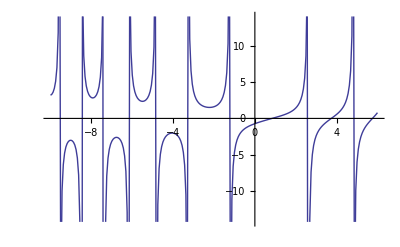

```mathematica
Monitor[TablePlot[p2[x]//Re,{x,-10.,6.,2.^(-4)}],x]
```

## Complex-valued example

Here's an example where the solution is complex valued

```mathematica
p3[x_]:=p3[x]=PainleveII[{1,2,1/3},x];
```

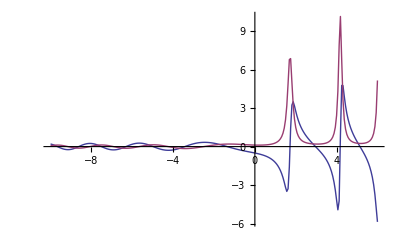

```mathematica
Monitor[ReImTablePlot[p3[x],{x,-10.,6.,2.^(-4)},PlotRange->All],x]
```

## References

A. S. Fokas, A. R. Its, A. A. Kapaev & V. Yu. Novokshenov (2006), Painlevé Transcendents: the Riemann–Hilbert approach, AMS. 

S. Olver (2010), A general framework for solving Riemann–Hilbert problems numerically, Report no. NA-10/5, Mathematical Institute, Oxford University.

S. Olver (2009b), Numerical solution of Riemann–Hilbert problems: Painlevé II, Report no. NA-09/9, Mathematical Institute, Oxford University.

S. Olver (2009a), Computing the Hilbert transform and its inverse, to appear in Maths Comp.